0.929168

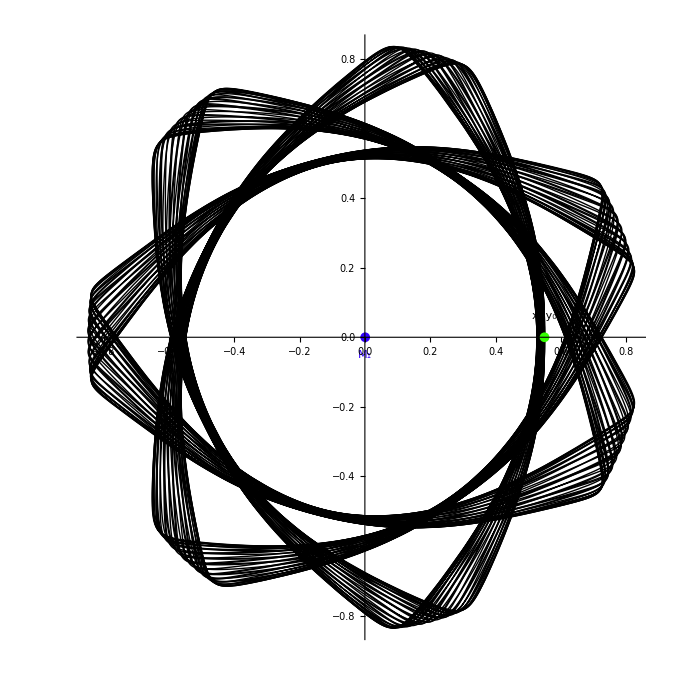

{{x[t]→1.06883,y[t]→0},{x[t]→0.932363,y[t]→0},{x[t]→-1.0004,y[t]→0}}

3.07

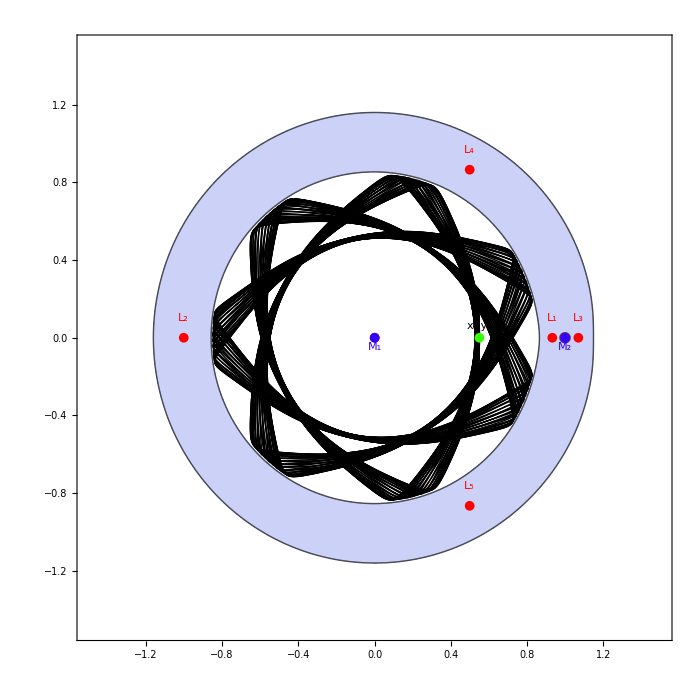

```mathematica
Clear["Global`*"];
Needs["DifferentialEquations`NDSolveProblems`"];
Needs["DifferentialEquations`NDSolveUtilities`"]
Needs["DifferentialEquations`InterpolatingFunctionAnatomy`"];
Needs["GUIKit`"];

(*tfin = 100.;
u =0.5;
x0 = 0.3;
y0 = 0.;
vx0 = 0.;
vy0 = 1.781; *)

u=0.000954;
(*********************************************************************)
 T=3.07;
x0=0.55;
y0=0.;
vx0=0.;
vy0 = N[Sqrt[(2-2u)/(√((u+x0)^2+y0^2))+(2u)/(√((-1+u+x0)^2+y0^2))+(x0^2+y0^2)-T-vx0^2]]

tfin=1000.; 


PMotion[mu1_,{x0_,y0_,vx0_,vy0_},tmax_,step_]:=
Module[{rrule,Urule,eqMotion,r1,r2,mu,U},
rrule={r1->Sqrt[(mu+x[t])^2+y[t]^2],
r2->Sqrt[(-1+mu+x[t])^2+y[t]^2]};
Urule={U->(1-mu)/r1+mu/r2+0.5(x[t]^2+y[t]^2)};

eqMotion=
{x''[t]-2y'[t]==D[U/.Urule/.rrule,x[t]],
y''[t]+2x'[t]==D[U/.Urule/.rrule,y[t]]};
(* se voglio TUTTE LE ORBITE  *)
NDSolve[{eqMotion/.mu->mu1,x[0]==x0,
y[0]==y0,x'[0]==vx0,y'[0]==vy0}//
Flatten,{x,y},{t,0,tmax},   Method -> {"ExplicitRungeKutta", "DifferenceOrder" -> 9},
MaxSteps->step]//Flatten]; 
(* se voglio OGNI 2Pi PERIODO  Mgraph[...]:=ListPlot[Table[{fx[t],fy[t]}//Evaluate,{t,0,tfinal,2 Pi}],AspectRatio->Automatic]*)

Mgraph[fx_,fy_,t_,tfinal_,Opts___]:=
ParametricPlot[{fx[t],fy[t]}//Evaluate,
{t,0,tfinal},
Opts,
AspectRatio->Automatic,
DisplayFunction->Identity]
(*Protect[PMotion,Mgraph];*)

sol=PMotion[u,{x0,y0,vx0,vy0},tfin,Infinity];
fx[t_]:=x[t]/.sol;
fy[t_]:=y[t]/.sol;

pt1=Mgraph[fx,fy,t,tfin,
PlotPoints->1000,
PlotStyle->Black,
Epilog->{
{
AbsolutePointSize[7], Hue[0.7],
Text["\!\(\*SubscriptBox[\(M\), \(1\)]\)",{u,-0.05}],
Text["\!\(\*SubscriptBox[\(M\), \(2\)]\)",{1-u,-0.05}],
{Point[{u,0}],Point[{1-u,0}]}
}
,
{
AbsolutePointSize[7],Hue[0.3],
Point[{x0,y0}]},
Text["\!\(\*SubscriptBox[\(x\), \(0\)]\),\!\(\*SubscriptBox[\(y\), \(0\)]\)",{x0,y0+0.06}]
}
,
DisplayFunction->$DisplayFunction,
ImageSize->700]

(*Export["solomotoRison.jpg",pt1]*)

Urule=U->(1-mu)/r1+mu/r2+0.5 (x[t]^2+y[t]^2);
rrule={r1->(√((mu+x[t])^2+y[t]^2)),
r2->(√((-1+mu+x[t])^2+y[t]^2))};

{L[5],L[4]}=
{{x[t]->0.5*(1-2*mu),y[t]->-0.5*Sqrt[3]},
{x[t]->0.5*(1-2*mu),y[t]->0.5*Sqrt[3]}}/.
{mu->u};
eq1=
D[U/.Urule/.rrule,x[t]]==0/.mu->u/.y[t]->0 ;
eq2=
D[U/.Urule/.rrule,y[t]]==0/.mu->u/.y[t]->0 ;
eq3=
FindRoot[eq1[[1]]/.mu->u/.
y[t]->0,{x[t],#}]&/@{1,0.9,-1} ;

{L[3],L[1],L[2]}=
Outer[List,eq3,{y[t]->0}]//
Flatten//Partition[#,2]&
JLpt=L[#]&/@Range[5];
JLpt//ColumnForm ; 

(*DISEGNA I PUNTI*)


Lgraph=
Graphics[
{PointSize[0.01],RGBColor[1,0,0],
{Point[{u,0}],Point[{1-u,0}]},
{PointSize[0.01],RGBColor[1,0,0],
Map[Point,{x[t],y[t]}/.JLpt]},
Text[Subscript[L, #],{x[t],y[t]+0.1}/.
JLpt[[#]]]&/@Range[5]
}
]/.mu->u ;

jacobi=J==-(x'[t]^2+y'[t]^2)+2U;
T=(jacobi/.Urule/.rrule/.mu->u/.y[t]->y0/.x'[t]->vx0/.x[t]->x0/.y'[t]->vy0)[[2]] 

cont=ContourPlot[2U/.Urule/.rrule/.mu->u//
Evaluate,
{x[t],-1.5,1.5},{y[t], -1.5,1.5},
ContourShading->False, (* ANCHE SE METTEVI NONE era indifferente sono la stessa cosa*)
AspectRatio->Automatic,
Contours->{T},
(*ContourLabels->All,*)
PlotPoints->300,
Epilog->{
{
AbsolutePointSize[7], Hue[0.7],
Text["\!\(\*SubscriptBox[\(M\), \(1\)]\)",{u,-0.05}],
Text["\!\(\*SubscriptBox[\(M\), \(2\)]\)",{1-u,-0.05}],
{Point[{u,0}],Point[{1-u,0}]}
}
,
{
AbsolutePointSize[7],Hue[0.3],
Point[{x0,y0}]},
Text["\!\(\*SubscriptBox[\(x\), \(0\)]\),\!\(\*SubscriptBox[\(y\), \(0\)]\)",{x0,y0+0.06}]
}
,
DisplayFunction->$DisplayFunction,
ImageSize->700];

ev=2U/.Urule/.rrule/.mu->u//Evaluate ;
region=RegionPlot[ev<T,{x[t],-1.5,1.5},{y[t], -1.5,1.5},
AspectRatio->Automatic,
PlotPoints->100,
Epilog->{
{
AbsolutePointSize[7], Hue[0.7],
Text["\!\(\*SubscriptBox[\(M\), \(1\)]\)",{u,-0.05}],
Text["\!\(\*SubscriptBox[\(M\), \(2\)]\)",{1-u,-0.05}],
{Point[{u,0}],Point[{1-u,0}]}
}
,
{
AbsolutePointSize[7],Hue[0.3],
Point[{x0,y0}]},
Text["\!\(\*SubscriptBox[\(x\), \(0\)]\),\!\(\*SubscriptBox[\(y\), \(0\)]\)",{x0,y0+0.06}]
}
,
DisplayFunction->$DisplayFunction,
ImageSize->700];

gra=Show[region,pt1,cont,Lgraph,
DisplayFunction->$DisplayFunction,
ImageSize->700]                                                                                      
 (*Export["coJupiter.jpg",gra]*)
```

True

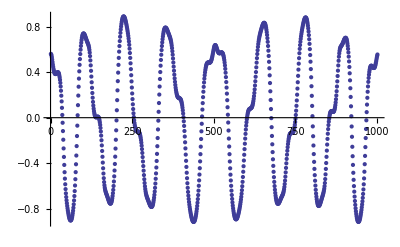

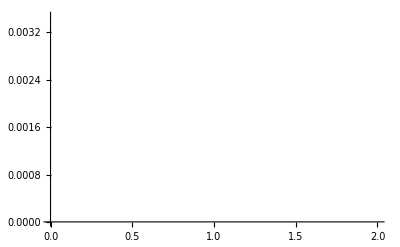

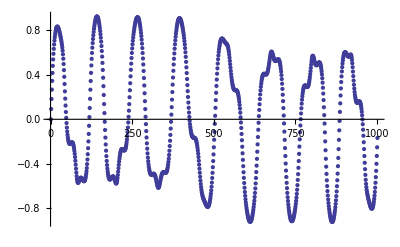

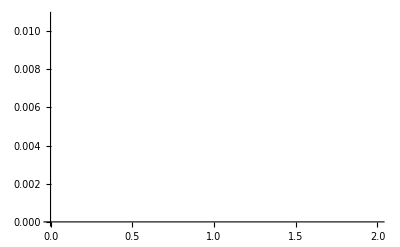

```mathematica
Clear["Global`*"];
m={X,Y,Vx,Vy}/.NDSolve[{
X'[t] == Vx[t],
Y'[t]== Vy[t],
Vx'[t] ==2 Vy[t]+X[t]-((1-mu) (mu+X[t]))/(((mu+X[t])^2+Y[t]^2)^(3/2))-(mu (-1+mu+X[t]))/(((-1+mu+X[t])^2+Y[t]^2)^(3/2)),
Vy'[t]== -2 Vx[t]+Y[t]-((1-mu) Y[t])/(((mu+X[t])^2+Y[t]^2)^(3/2))-(mu Y[t])/(((-1+mu+X[t])^2+Y[t]^2)^(3/2)),
X[0]== 0.56,Vx[0]== 0.,Y[0]==0.,Vy[0]== 0.929168}/.{mu->0.000954},{X,Y,Vx,Vy},{t,0.,100.},MaxSteps->100000]⟦1⟧;
data1=Table[Evaluate[m[[#]][t]&/@{1,2}],{t,0.,100.,0.1}];
dataX=Table[Evaluate[m[[#]][t]&/@{1}],{t,0.,100.,0.1}];
dataY=Table[Evaluate[m[[#]][t]&/@{2}],{t,0.,100.,0.1}];

Export["Cor56.dat",data1];
data2=Import["Cor56.dat"];
(*FilePrint["data1.dat"]*)
data1==data2
ListPlot[Transpose@dataX,Filling->None]
ListLinePlot[Abs[Fourier[dataX]]]
ListPlot[Transpose@dataY,Filling->None]
ListLinePlot[Abs[Fourier[dataY]]]
(*ListPlot[Transpose@data2,Filling->None]*)
Graphics[Point[data2]];
```

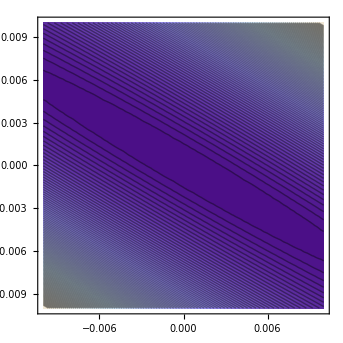
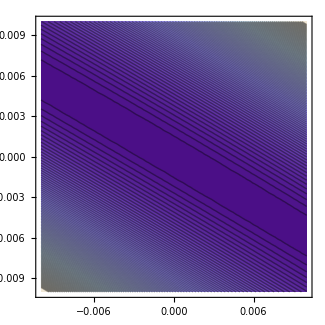
{-Graphics-,-Graphics-,-Graphics-}

```mathematica
u = 0.01;
xc = 0.5-u;
yc = Sqrt[3]/2; 
xxc = 0.;
yyc = 0.;
alfa =(3/4)*Sqrt[3]*(1-2*u);

UAp= (3/8)*(x)^2+(9/8)*(y)^2+alfa*(x)*(y);

Plot3D[UAp,{x,-0.01,0.01},{y,-0.01,0.01}];
Plot3D[UEx,{x,-0.1,0.1},{y,-0.01,0.01}];
{ContourPlot[UAp,{x,-0.01,0.01},{y,-0.01,0.01},Contours->100],
ContourPlot[UEx,{x,-0.01,0.01},{y,-0.01,0.01},Contours->100],ContourPlot[Log10[Abs[UEx-UAp]/(UEx)],{x,-0.01,0.01},{y,-0.01,0.01},Contours->100]};
r1=(√((u+x+xc)^2+(y+yc)^2));
r2=(√((-1+u+x+xc)^2+(y+yc)^2));
UEx=(1-u)/r1+u/r2+0.5 ((x+xc)^2+(y+yc)^2)-1-0.5(xc^2+yc^2);
```

```mathematica
u = 0.001;
xc = 0.5-u;
yc = Sqrt[3]/2; 
xxc = 0.;
yyc = 0.;
alfa =(3/4)*Sqrt[3]*(1-2*u);

UAp= (3/8)*(x)^2+(9/8)*(y)^2+alfa*(x)*(y);
r1=(√((u+x+xc)^2+(y+yc)^2));
r2=(√((-1+u+x+xc)^2+(y+yc)^2));
UEx=(1-u)/r1+u/r2+0.5 ((x+xc)^2+(y+yc)^2)-1-0.5(xc^2+yc^2);

Plot3D[UAp,{x,-0.01,0.01},{y,-0.01,0.01}]
Plot3D[UEx,{x,-0.01,0.01},{y,-0.01,0.01}]
Plot3D[Log10[Abs[UEx-UAp]/(UEx)],{x,-0.01,0.01},{y,-0.01,0.01}]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

-Graphics3D-

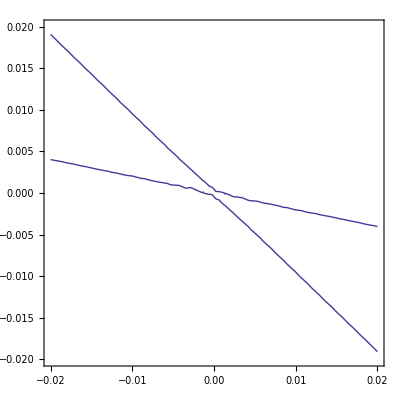

```mathematica
ContourPlot3D[4*(y^2+z^2)-3*x^2+3*x0^2==0,{x,-0.02,0.02},{y,-0.02,0.02},{z,-0.02,0.02}];
ContourPlot[y^2- (3/8)*x^2==-(3/8)*x0^2,{x,-2,2},{y,-2,2},Contours->10];



x0 =0.001;
y0 =0.;
u = 0.001;

alfa1 =6*Sqrt[3]*(1-2*u);

ContourPlot3D[4*z^2-Sqrt[3]*x^2-9*y^2-6*Sqrt[3]*x*y==-3*x0^2,{x,-0.02,0.02},{y,-0.02,0.02},{z,-0.02,0.02}]
ContourPlot[-Sqrt[3]*x^2-9*y^2-6*Sqrt[3]*x*y==-3*x0^2,{x,-0.02,0.02},{y,-0.02,0.02}]
```

```mathematica
TableForm[ParallelEvaluate[{$KernelID,$MachineName,$SystemID,$VersionNumber,$ProcessID,TimeUsed[], MaxMemoryUsed[],"ProcessPriority"/.SystemOptions["ProcessPriority"]}],TableHeadings->{None,{"ID","host", "OS","Version", "Process","CPU Time","Memory", "Priority"}},TableDepth->2]
```

ID | host | OS | Version | Process | CPU Time | Memory | Priority
1 | utente-pc | Windows-x86-64 | 9. | 4536 | 0.203 | 21106792 | BelowNormal
2 | utente-pc | Windows-x86-64 | 9. | 1500 | 0.187 | 21106792 | BelowNormal